```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
```

```mathematica
FitError[func_,list_,p_]:=Module[{tab1,nbin},
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}];
If[p==Null,
tab1=Table[(list[[i,2]]-func[list[[i,1]]])^2,{i,1,Length[list]}],
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}]
];
nbin=Length[tab1];
√(Total[tab1]/(nbin-1))
]
```

```mathematica
SemiPoisson[s_]:=4 s Exp[-2 s]
```

```mathematica
porterthomas[x_]:=Exp[-x/2]/(√(2π x))
```

```mathematica
genpt[x_,ν_]:=(ν/2 x)^(ν/2-1)/Gamma[ν/2] ν/2 Exp[-ν/2 x]
```

```mathematica
genpt[x,1]
```

ⅇ^(-x/2)/(√(2 π) √x)

```mathematica
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.800","Table"];*)
AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];
AWD=DeleteCases[DeleteCases[AllWidthData,AllWidthData[[1]]],{}];
WidthData[ic_,E1_,E2_]:=Select[AWD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];
Select[AWD,(#1[[7]]>10^-1)&]
```

{}

```mathematica
iens=1;icoup=2;
```

```mathematica
(*path1=StringJoin[{"~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.",ToString[iens*1000+icoup]}]*)
path1=StringJoin[{"~/Code/Nchannel/Square/CODES/fort.",ToString[iens*1000+icoup]}]
```

~/Code/Nchannel/Square/CODES/fort.1002

```mathematica
Data=DeleteCases[Import[path1,"Table"],{}];
```

```mathematica
iemax=Length[Data];iemin=1;
sigma=Table[{Data[[ie,2]],Data[[ie,10]]},{ie,iemin,iemax}];
lzclose=Table[{Data[[ie,2]], Log[Data[[ie,6]]]},{ie,iemin,iemax}];
alsqr=Table[{Data[[ie,2]],Data[[ie,5]]},{ie,iemin,iemax}];
albgsqr=Table[{Data[[ie,2]],Sin[Data[[ie,8]]]^2},{ie,iemin,iemax}];
phaseopi=Table[{Data[[ie,2]],Data[[ie,11]]},{ie,iemin,iemax}];
ltimedelay=Table[{Data[[ie,2]],Log[Data[[ie,12]]]},{ie,iemin,iemax}];
ascat = Table[{Data[[ie,2]],Data[[ie,4]]},{ie,iemin,iemax}];
abg=  Table[{Data[[ie,2]],Data[[ie,13]]},{ie,iemin,iemax}];
BSdet = Table[{Data[[ie,2]],Data[[ie,7]]},{ie,iemin,iemax}];
```

```mathematica
padding={{100,45},{80,0}};
imgsize={600,300};
yrange=All;
xrange={0,1.01 10^-1};
aspctratio=Full;1/GoldenRatio;
pabg=ListPlot[abg,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a_bg/r_0"},LabelStyle->{16},PlotRange->{xrange,{-1000,1000}},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
palsqr=ListPlot[{alsqr,albgsqr},Joined->True,PlotStyle->{{Black},{Red,Dotted}},Frame->True,FrameLabel->{"E/(ℏ^2/2μ r_0^2)",TraditionalForm[Sin[δ]^2]},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio,FrameTicks->{Automatic,Automatic}];
psigma=ListPlot[sigma,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","σ/r_0^2"},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
pstair=ListPlot[phaseopi,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","δ_0/π"},LabelStyle->{16},PlotRange->{xrange,All},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
plzc=ListPlot[lzclose,Joined->True,PlotStyle->{Red,Dashed},Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","log(Z_C)"},LabelStyle->{16},PlotRange->{xrange,{-5,18}},GridLines->Automatic,ImageSize->{600,250},ImagePadding->{{100,45},{8,8}},AspectRatio->aspctratio,ImageMargins->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
pltd=ListPlot[ltimedelay,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{(*"E/(ℏ^2/2μr_0^2)"*)None,TraditionalForm[Log[(τ ℏ)/(2μ Subscript[r, 0]^2)]]},LabelStyle->Large,PlotRange->{xrange,{-5,18}},GridLines->Automatic,FrameTicks->{Automatic,Automatic},ImageSize->{600,250},ImagePadding->{{100,45},{8,8}},AspectRatio->aspctratio,ImageMargins->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
pascat=ListPlot[ascat,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a/r_0"},LabelStyle->{16},PlotRange->{xrange,{-100,100}},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
```

```mathematica
pbsdet=ListPlot[BSdet,Joined->True,PlotStyle->Black,Frame->True,LabelStyle->{16},PlotRange->{xrange,{-10^-100,10^-100}},AspectRatio->50/1000,ImageSize->{600,50},PlotRangeClipping->False,ImagePadding->{{100,45},{0,20}},FrameTicks->{None,None},ImageMargins->0,Axes->False,Epilog->{Text[Style["(a)",Bold,22],{-20.,0}]}]
```

-Graphics-

```mathematica
(*AllResData=DeleteCases[Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.800","Table"],{}];*)
AllResData=DeleteCases[Import["~/Code/Nchannel/Square/CODES/fort.800","Table"],{}];
ResData[iens_,icoup_]:=Select[Select[AllResData,(#[[2]]==iens)&],(#[[3]]==icoup)&]
Resonances = ResData[iens,icoup];
NumRes=Length[Resonances];

ResLines=Table[ssbg  (EE-ER+q Γ/2)^2/((EE-ER)^2+(Γ/2)^2)/.{ssbg->Resonances[[ires,9]],ER->Resonances[[ires,5]],Γ->Resonances[[ires,7]],q->Resonances[[ires,8]]},{ires,1,NumRes}];
resplots=Table[Plot[Evaluate[ResLines[[ires]]],{EE,Resonances[[ires,5]]-2Resonances[[ires,7]],Resonances[[ires,5]]+2Resonances[[ires,7]]},PlotStyle->{Blue,Dashed},PlotRange->All,ImagePadding->padding,ImageSize->imgsize,AspectRatio->Full],{ires,1,NumRes}];
```

```mathematica
widthdata=Table[{Resonances[[ires,5]],Resonances[[ires,7]]},{ires,1,NumRes}];
qdata=Table[{Resonances[[ires,5]],Resonances[[ires,8]]},{ires,1,NumRes}];
```

```mathematica
pwidth=ListPlot[widthdata,PlotStyle->Black,Frame->True,LabelStyle->Medium,FrameLabel->{"E","Γ/(ℏ^2/2μr_0^2)"}];
```

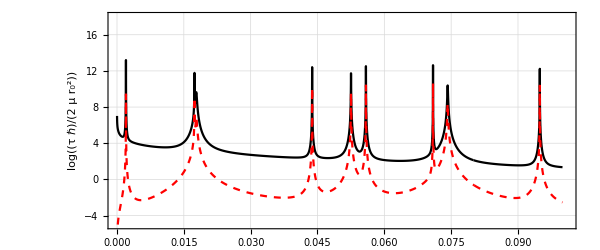

```mathematica
ptdlz=Show[{pltd,plzc},PlotRange->{xrange,{-5,18}},FrameLabel->{{TraditionalForm[Log[(τ ℏ)/(2μ Subscript[r, 0]^2)] ],TraditionalForm[Style[Log[Subscript[Z, C]],Red]]},{None,None}},PlotRangeClipping->False,Epilog->{Text[Style["(b)",Bold,22],{-1.5,9.5}]}]
```

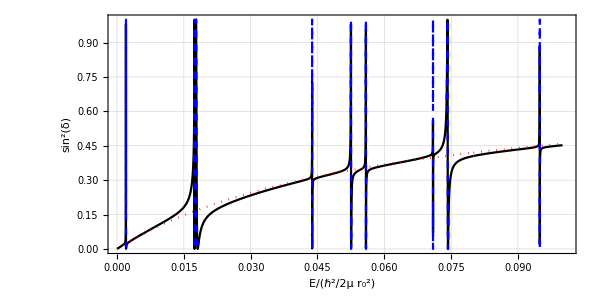

```mathematica
pfanolines = Show[{palsqr,resplots},PlotRange->{xrange,{0,1}},LabelStyle->Large,PlotRangeClipping->False,Epilog->{Text[Style["(c)",Bold,22],{-1.5,0.9}]}]
```

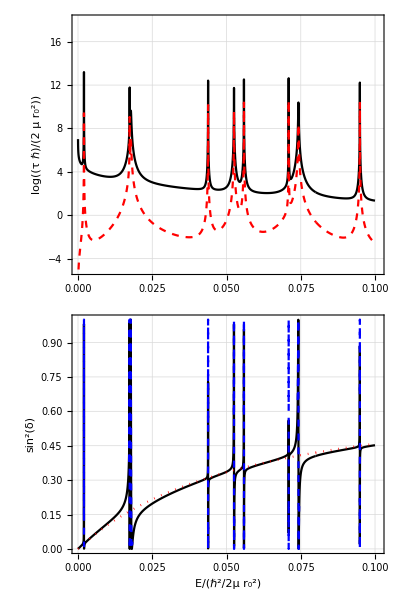

```mathematica
p1=Grid[{{pbsdet},{ptdlz},{pfanolines}},Spacings->0]
```

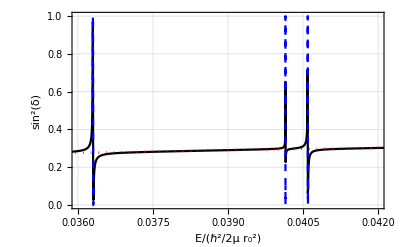

```mathematica
pfanofits=Show[pfanolines,PlotRange->{{0.036,0.042},All},ImagePadding->Automatic,ImageSize->Automatic,AspectRatio->1/GoldenRatio,PlotRangeClipping->True]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-fanofits.pdf",pfanofits]
```

~/Code/Nchannel/Square/CODES/plots/p-fanofits.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-poisson-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-poisson-scat.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-wigner-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-wigner-scat.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-tridiag-chris-3chan-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-tridiag-chris-3chan-scat.pdf

### Statistical Data

```mathematica
Emin=0.0;Emax=0.1;
```

```mathematica
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.800","Table"];*)
AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];
```

```mathematica
AWD=DeleteCases[DeleteCases[AllWidthData,AllWidthData[[1]]],{}];
remove=Position[AWD,u_/;(u[[7]]>  10^-0)]
AWDTrimmed=Delete[AWD,remove];
```

Part::partd: Part specification List⟦7⟧ is longer than depth of object.

Part::partd: Part specification 1⟦7⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{}

```mathematica
WidthData[ic_,E1_,E2_]:=Select[AWDTrimmed,(#1[[3]]==ic && E1<#1[[5]]<E2)&];
```

```mathematica
ic=1;
WDtest=WidthData[ic,Emin,Emax];
```

```mathematica
Select[AWDTrimmed,(#1[[7]]>10^0)&]
```

{}

```mathematica
db=0.2;bins=Table[x,{x,0,5,db}];
bfit=Table[0.5(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}]
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9,3.1,3.3,3.5,3.7,3.9,4.1,4.3,4.5,4.7,4.9}

```mathematica
(*Sdat=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.700","Table"];*)
Sdat=Import["~/Code/Nchannel/Square/CODES/fort.700","Table"];
SD=DeleteCases[Sdat,Sdat[[1]]];
```

```mathematica
(*ic=50;
WDtest=Select[AWDTrimmed,(#1[[3]]==ic)&];*)
```

```mathematica
nw=Length[WDtest]
```

100

```mathematica
Warray=Table[WDtest[[i,7]]/(√WDtest[[i,5]]),{i,1,nw}];
```

```mathematica
meanw=Mean[Warray]
```

0.000427021

```mathematica
Median[Warray]
```

0.000225022

```mathematica
Wscaled=Warray/meanw;
```

```mathematica
wc1=BinCounts[Wscaled,{bins}]
```

{31,10,13,6,5,3,4,5,1,3,2,2,5,1,2,0,2,1,1,0,0,2,1,0,0}

```mathematica
wcnorm=Table[{bins[[i]],wc1[[i]]/nw/db},{i,1,Length[bins]-1}];
```

```mathematica
ν0=0.5;
wcfit=Table[{bfit[[i]],wcnorm[[i,2]]},{i,1,Length[wcnorm]}];
ph=ListPlot[wcnorm,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black];
nlm=NonlinearModelFit[wcfit,{genpt[γ,ν]},{{ν,1.0}},γ,Method->"LevenbergMarquardt",ConfidenceLevel->0.99]
pgenpt=Plot[genpt[γ,ν/.nlm["BestFitParameters"]],{γ,0,5},PlotStyle->{Red},PlotRange->All];
```

FittedModel[(0.385885 ⅇ^(-0.485482 γ))/γ^0.514518]

```mathematica
nlm["BestFitParameters"]
```

{ν→0.970965}

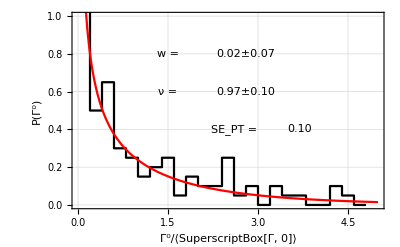

```mathematica
pporterthomas=Show[{ph,pgenpt},PlotRange->{0,1},Frame->True,GridLines->Automatic,FrameLabel->{"Γ^0/⟨SuperscriptBox[Γ, 0]⟩","P(Γ^0)"},LabelStyle->Large,Epilog->{
Text[Style["w = ",Large],{1.5,0.8}],
Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{2.8,0.8}],
Text[Style["ν = ",Large],{1.5,0.6}],Text[Style[NumberForm[ν/.nlm["BestFitParameters"],{2,2}]±NumberForm[FitError[genpt,wcfit,ν/.nlm["BestFitParameters"]],{2,2}],Large],{2.8,0.6}],
Text[Style["SE_PT = ",Large],{2.6,0.4}],
Text[Style[NumberForm[FitError[porterthomas,wcfit,Null],{2,2}],Large],{3.7,0.4}],
(*Text[Style["SE_ad = ",Large],{2.0,0.2}]*),
(*Text[Style[NumberForm[FitError[pnpm,wcfit,Null],{2,2}],Large],{2.6,0.2}]*)}]
```

```mathematica
FitError[porterthomas,wcfit,Null]
```

0.106494

```mathematica
ν/.nlm["BestFitParameters"][[1]]
```

0.951502

```mathematica
FitError[genpt,wcfit,1]
```

0.108365

```mathematica
FitError[genpt,wcfit,ν/.nlm["BestFitParameters"][[1]]]
```

0.108345

```mathematica
1/(Length[bfit]-1)Covariance[wcfit[[1;;Length[wcfit],2]],Table[γ^(ν/2-1)/Gamma[ν/2] Exp[-γ/2]/.{nlm["BestFitParameters"][[1]],γ->wcfit[[i,1]]},{i,1,Length[bfit]}]]
```

0.00538388

```mathematica
nlm["CovarianceMatrix"]
```

{{0.0475255}}

```mathematica
√nlm["CovarianceMatrix"]
```

{{0.218003}}

```mathematica
Total[nlm["FitResiduals"]^2]
```

0.281725

```mathematica
nlm["ParameterErrors"]
```

{0.218003}

### Distribution for the time delay

```mathematica
Integrate[(1/2)^(M/2)Exp[-M /(2τ)]/(Gamma[M/2](M τ)^((M+4)/2))/.M->1,{τ,0,∞}]
```

1

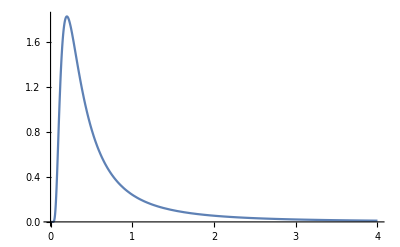

```mathematica
Plot[(1/2)^(M/2)Exp[-M /(2τ)]/(Gamma[M/2](M τ)^((M+4)/2))/.M->1,{τ,0,4},PlotRange->All]
```

```mathematica
ic=1;
WDtest=Select[AWD,(#1[[3]]==ic)&];
```

```mathematica
nw=Length[WDtest]
```

3996

```mathematica
tdarray=Table[4/WDtest[[i,7]],{i,1,nw}];
```

```mathematica
tdarray[[1]]
```

859328.

```mathematica
meantd=Mean[tdarray]
```

2.13676×10^8

```mathematica
Median[tdarray]
```

469528.

```mathematica
{Min[tdarray],Max[tdarray]}
```

{6622.52,3.02755×10^11}

```mathematica
dtb=0.1;tbins=Table[i,{i,0,4,dtb}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.}

```mathematica
tbinfit=Table[(tbins[[i]]+tbins[[i+1]])/2,{i,1,Length[tbins]-1}]
```

{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95}

```mathematica
td1=BinCounts[tdarray/meantd,{tbins}]
```

{3684,94,37,30,22,8,16,11,7,3,2,2,0,3,6,2,4,1,2,3,5,4,2,2,1,0,0,0,0,0,4,1,1,2,2,0,0,0,0,0}

```mathematica
tdfit=Table[{tbinfit[[i]],td1[[i]]/nw/dtb},{i,1,Length[wcnorm]}];
```

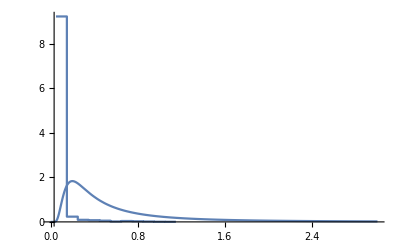

```mathematica
Show[{ListPlot[tdfit,InterpolationOrder->0,Joined->True,PlotRange->All],Plot[(1/2)^(M/2)Exp[-M /(2τ)]/(Gamma[M/2](M τ)^((M+4)/2))/.M->1,{τ,0,3}]},PlotRange->All]
```

Well... that doesn’t seem right at all.

### Zclose vs. width

```mathematica
gammazc[ic_,E1_,E2_]:=Module[{WidthData,i,nw},
WidthData=Select[AWD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];(*Select[AWDTrimmed,(#1[[3]]==ic )&];*)
nw=Length[WidthData];
Table[{WidthData[[i,7]]/√WidthData[[i,5]],WidthData[[i,6]]},{i,1,nw}]
]
```

```mathematica
Allgammazc=Table[{AWDTrimmed[[i,7]]/√AWDTrimmed[[i,5]],AWDTrimmed[[i,6]]},{i,1,Length[AWDTrimmed]}];
```

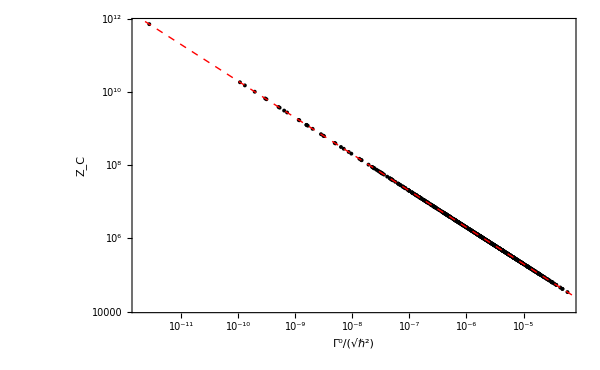

```mathematica
pgammazc=Show[{ListLogLogPlot[Allgammazc,Frame->True,LabelStyle->{Large},PlotMarkers->{"●",4.0},PlotStyle->{Small,Black},FrameLabel->{TraditionalForm["Γ^0"/"√(ℏ^2)"],TraditionalForm[Subscript[Z, C]]},ImageSize->{600,600/1.6}],LogLogPlot[A (x)^b/.{A->2,b->-1},{x,10^-13,10^-0},PlotStyle->{Red,Dashed,Thin}]}]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pgammazc.pdf",pgammazc]
```

~/Code/Nchannel/Square/CODES/plots/pgammazc.pdf

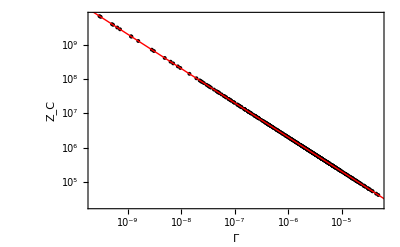

```mathematica
Show[{ListLogLogPlot[gammazc[1,0.0,.1],Frame->True,LabelStyle->Large,PlotMarkers->{"●",4.0},PlotStyle->{Small,Black},FrameLabel->{TraditionalForm[Γ],TraditionalForm[Subscript[Z, C]]}],
(*ListLogLogPlot[gammazc[2],Frame->True,LabelStyle->Large,PlotMarkers->{"●",2.0},PlotStyle->{Small,Blue},FrameLabel->{TraditionalForm[Γ],TraditionalForm[Subscript[Z, C]]}],*)
LogLogPlot[A (x)^b/.{A->2,b->-1},{x,10^-12,10^1},PlotStyle->{Red,Thin}]}]
```

```mathematica
Spoles[ic_,E1_,E2_]:=Module[{WidthData,i,nw},
WidthData=Select[AWD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];(*Select[AWD,(#1[[3]]==ic )&];*)
nw=Length[WidthData];
Table[{WidthData[[i,5]],WidthData[[i,7]]/(√WidthData[[i,5]])},{i,1,nw}]
]
```

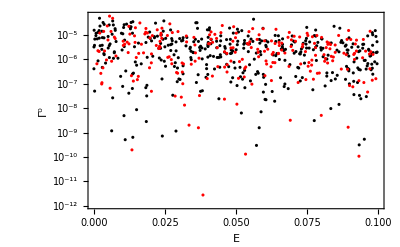

```mathematica
Dom={0.0,0.1};ListLogPlot[{Spoles[1,Dom[[1]],Dom[[2]]],Spoles[2,Dom[[1]],Dom[[2]]]},Frame->True,LabelStyle->Large,PlotStyle->{{Black,Small},{Red,Small}},FrameLabel->{TraditionalForm["E"],TraditionalForm["Γ^0"]},PlotRange->{Dom,All}]
```

```mathematica
(*Sdat=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.700","Table"];*)
Sdat=Import["~/Code/Nchannel/Square/CODES/fort.700","Table"];
SD=DeleteCases[Sdat,Sdat[[1]]];
```

```mathematica
Length[SD]
```

2

```mathematica
brodydata=Table[{{SD[[i,5]],SD[[i,7]]},ErrorBar[SD[[i,8]]]},{i,1,Length[SD]}];
gocdata=Table[{SD[[i,5]],SD[[i,4]]},{i,1,Length[SD]}];
```

```mathematica
brodydata0=Table[{brodydata[[i,1,1]],brodydata[[i,1,2]]},{i,1,Length[brodydata]}];
brodydatap=Table[{brodydata[[i,1,1]],brodydata[[i,1,2]]+Part[brodydata[[i,2]],1]},{i,1,Length[brodydata]}];
brodydatam=Table[{brodydata[[i,1,1]],brodydata[[i,1,2]]-Part[brodydata[[i,2]],1]},{i,1,Length[brodydata]}];
```

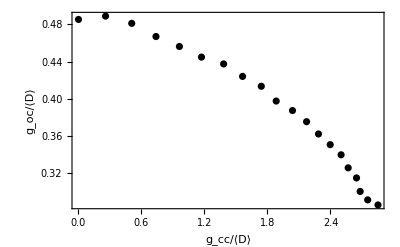

```mathematica
pgocplot=ListPlot[gocdata,PlotStyle->Black,Frame->True,FrameLabel->{"g_cc/⟨D⟩","g_oc/⟨D⟩"},LabelStyle->Medium]
```

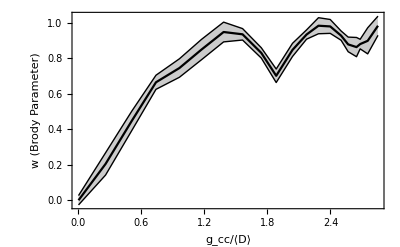

```mathematica
pbrody1=ListPlot[{brodydatam,brodydata0,brodydatap},Frame->True,PlotStyle->{{Black,Thin},{Black},{Black,Thin}},Filling->{1->{3}},Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","w (Brody Parameter)"},GridLines->None,PlotRange->All,Epilog->{Inset[pgocplot,{1.6,.30},{Automatic,Automatic},{1.5,Automatic}]}]
```

```mathematica
bfit
```

{0.1,0.3,0.5,0.7,0.9,1.1,1.3,1.5,1.7,1.9,2.1,2.3,2.5,2.7,2.9,3.1,3.3,3.5,3.7,3.9,4.1,4.3,4.5,4.7,4.9}

```mathematica
nufitdata=Table[WDtemp=WidthData[ic,0.0,0.1];
nw=Length[WDtemp];
Warray=Table[WDtemp[[i,7]],{i,1,nw}];
meanw=Mean[Warray];
wc1=BinCounts[Warray/meanw,{bins}];
wcnorm=Table[{bins[[i]],wc1[[i]]/nw/db},{i,1,Length[bins]-1}];
ν0=0.954;
wcfit=Table[{bfit[[i]],wcnorm[[i,2]]},{i,1,Length[wcnorm]}];
nlm=NonlinearModelFit[wcfit,{genpt[γ,ν]},{{ν,1.0}},γ,Method->Automatic,ConfidenceLevel->0.999];
{{SD[[ic,5]],ν/.nlm["BestFitParameters"]},ErrorBar[FitError[genpt,wcfit,ν/.nlm["BestFitParameters"]]](*ErrorBar[nlm["ParameterErrors"][[1]]]*)},{ic,1,Length[SD]}];
```

```mathematica
Graphics`PlotMarkers[]
```

```mathematica
l1=ImageCrop[Graphics[{Red,Thick,Line[{{0,0},{.1,0}}]}]]
```

-Graphics-

```mathematica
l2=ImageCrop[Graphics[{Black,Thick,Line[{{0,0},{.1,0}}]}]]
```

-Graphics-

```mathematica
nufitdata0=Table[{nufitdata[[i,1,1]],nufitdata[[i,1,2]]},{i,1,Length[nufitdata]}];
nufitdatap=Table[{nufitdata[[i,1,1]],nufitdata[[i,1,2]]+Part[nufitdata[[i,2]],1]},{i,1,Length[nufitdata]}];
nufitdatam=Table[{nufitdata[[i,1,1]],nufitdata[[i,1,2]]-Part[nufitdata[[i,2]],1]},{i,1,Length[nufitdata]}];
```

```mathematica
nuplot1=ListPlot[{nufitdatam,nufitdata0,nufitdatap},Frame->True,LabelStyle->Large,PlotStyle->{{Red,Thin},{Red},{Red,Thin}},Joined->True,PlotRange->{0,1.1},Joined->True,Filling->{1->{3}}];
```

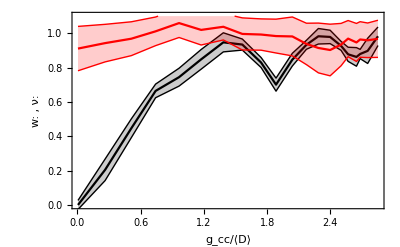

```mathematica
pbrody=Show[{pbrody1,nuplot1},PlotRange->{0,1.1},FrameLabel->{"g_cc/⟨D⟩","w: , ν: "}]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pbrody.pdf",pbrody]
```

~/Code/Nchannel/Square/CODES/plots/pbrody.pdf

```mathematica
(*Posdata=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.500","Table"];*)
Posdata=Import["~/Code/Nchannel/Square/CODES/fort.500","Table"];
Posdata=DeleteCases[Posdata,Posdata[[1]]];
Posdata[[1]]
```

{1,1,0.0088023,1.1361,1.1361×10^-8,0.0094581,0.019929,0.074058,0.85393,0.76404,0.49438,0.31461,0.31461,0.31461,0.40449,0.13483,0.044944,0.22472,0.,0.,0.,0.089888,0.,0.,0.044944,0.,0.,0.}

```mathematica
dxp=5/20.;
pbins=Table[x,{x,0,5,dxp}];
```

```mathematica
pfitbins=Table[0.5*(pbins[[i]]+pbins[[i+1]]),{i,1,Length[pbins]-1}]
```

{0.125,0.375,0.625,0.875,1.125,1.375,1.625,1.875,2.125,2.375,2.625,2.875,3.125,3.375,3.625,3.875,4.125,4.375,4.625,4.875}

```mathematica
Posdata[[1]]
```

{1,1,0.0088023,1.1361,1.1361×10^-8,0.0094581,0.019929,0.074058,0.85393,0.76404,0.49438,0.31461,0.31461,0.31461,0.40449,0.13483,0.044944,0.22472,0.,0.,0.,0.089888,0.,0.,0.044944,0.,0.,0.}

```mathematica
yrange={0,1.0};
impad1={{80,10},{95,5}};
ic=1;
pnorm=Table[{pbins[[i]],Posdata[[ic,i+8]]},{i,1,20}];
pfit=Table[{pfitbins[[i]],pnorm[[i,2]]},{i,1,20}];
```

```mathematica
FitError[SemiPoisson,pfit,Null]
```

0.152959

```mathematica
options1={PlotRange->{All,yrange},Frame->True,GridLines->Automatic,FrameLabel->{TraditionalForm[S/⟨D⟩],TraditionalForm[P[S]]},LabelStyle->Large,ImageSize->{450,300},ImagePadding->impad1,FrameTicksStyle->{None,Automatic},AspectRatio->Full};ppoisson=Show[ListPlot[pnorm,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black],Plot[PBrody[x,SD[[ic,7]]],{x,0,5},PlotStyle->Red],options1,Epilog->{Text[Style["w = ",Large],{2.5,0.5}],Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{3.9,0.5}],Text[Style["(a)",20,Bold],{.2,.93}]}];
```

```mathematica
ic=1;
impad2={{80,10},{5,5}};
pnorm=Table[{pbins[[i]],Posdata[[ic,i+8]]},{i,1,20}];
options={PlotRange->{All,yrange},Frame->True,GridLines->Automatic,FrameLabel->{None,TraditionalForm[P[S]]},LabelStyle->Large,ImageSize->{450,200},ImagePadding->impad2,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},AspectRatio->Full};
pwigner=Show[ListPlot[pnorm,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black],Plot[PBrody[x,SD[[ic,7]]],{x,0,5},PlotStyle->Red],options,Epilog->{Text[Style["w = ",Large],{2.5,0.5}],Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{3.9,0.5}],Text[Style["(c)",20,Bold],{.2,.93}]}];
```

```mathematica
ic=2;
pnorm=Table[{pbins[[i]],Posdata[[ic,i+8]]},{i,1,20}];
pfit=Table[{pfitbins[[i]],pnorm[[i,2]]},{i,1,20}];
pmiddle=Show[{ListPlot[pnorm,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black],Plot[PBrody[x,SD[[ic,7]]],{x,0,5},PlotStyle->Red],Plot[4 s Exp[-2 s],{s,0,5},PlotStyle->{Blue,Dashed}]},options,Epilog->{Text[Style["w = ",Large],{2.5,0.5}],Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{3.9,0.5}],Text[Style["SE_SP = ",Large],{3.0,0.3}],Text[Style[NumberForm[FitError[SemiPoisson,pfit,Null],{2,2}],Large],{3.9,0.3}],
Text[Style["(b)",20,Bold],{.2,.93}]},PlotRangeClipping->False];
```

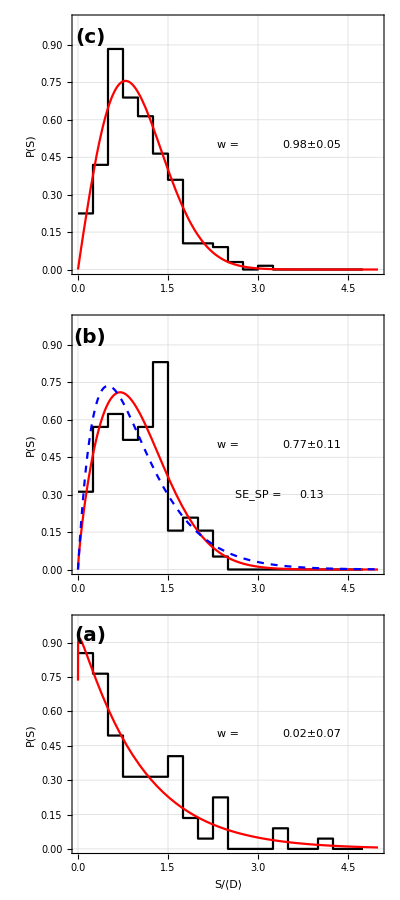

```mathematica
pstats=Grid[{{pwigner},{pmiddle},{ppoisson}},Spacings->0]
```

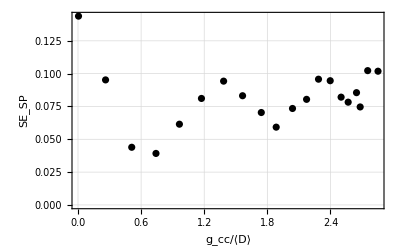

```mathematica
ListPlot[Table[
pnorm=Table[{pbins[[i]],Posdata[[ic,i+8]]},{i,1,20}];
pfit=Table[{pfitbins[[i]],pnorm[[i,2]]},{i,1,20}];
{SD[[ic,5]],FitError[SemiPoisson,pfit,Null]},{ic,1,20}],Frame->True,PlotStyle->Black,Joined->False,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","SE_SP"},GridLines->Automatic]
```

```mathematica
Table[{pfitbins[[i]],Posdata[[ic,i+8]]},{i,1,20}]
```

{{0.125,0.27373},{0.375,0.71523},{0.625,0.7064},{0.875,0.65342},{1.125,0.58278},{1.375,0.32671},{1.625,0.24724},{1.875,0.15894},{2.125,0.10596},{2.375,0.0883},{2.625,0.04415},{2.875,0.01766},{3.125,0.02649},{3.375,0.01766},{3.625,0.01766},{3.875,0.01766},{4.125,0.},{4.375,0.},{4.625,0.},{4.875,0.}}

```mathematica
ic=9;FitError[PBrody,Table[{pfitbins[[i]],Posdata[[ic,i+8]]},{i,1,20}],SD[[ic,7]]]
```

0.0291047

```mathematica
ic=9;FitError[SemiPoisson,Table[{pfitbins[[i]],Posdata[[ic,i+8]]},{i,1,20}],Null]
```

0.0425943

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pstats.pdf",pstats]
```

~/Code/Nchannel/Square/CODES/plots/pstats.pdf

### Width data...

```mathematica
avgwidths=Table[{SD[[i,5]],SD[[i,6]]SD[[i,3]]},{i,1,Length[SD]}];
```

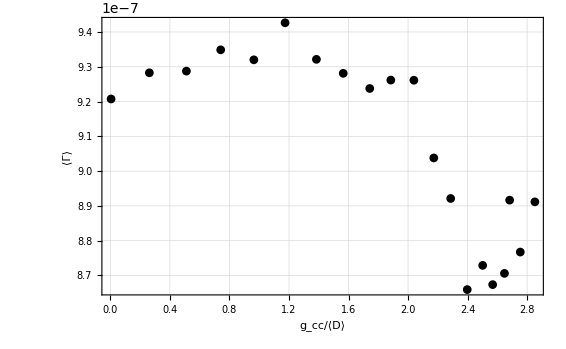

```mathematica
ListPlot[avgwidths,Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic,PlotRange->All,Joined->False,PlotMarkers->Automatic,FrameLabel->{"g_cc/⟨D⟩","⟨Γ⟩"}]
```

```mathematica
avgwidths2=Table[{SD[[i,4]],SD[[i,6]]},{i,1,Length[SD]}];
```

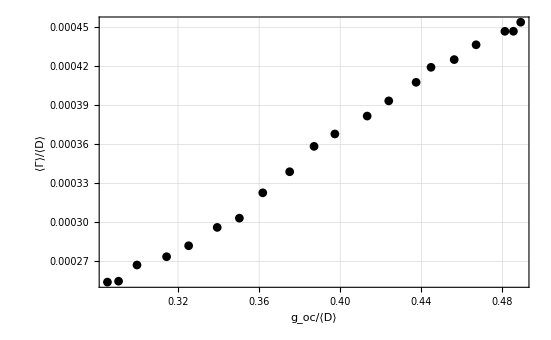

```mathematica
ListPlot[avgwidths2,Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic,PlotRange->All,Joined->False,PlotMarkers->Automatic,FrameLabel->{"g_oc/⟨D⟩","⟨Γ⟩/⟨D⟩"}]
```

```mathematica
MeanW[EE_,WindowE_,ic_]:=Module[{WidthData,i,nw,w},
WidthData=Select[AWDTrimmed,(#1[[3]]==ic && EE<#1[[5]]<EE+WindowE)&];
nw=Length[WidthData];
w=Table[WidthData[[i,7]],{i,1,nw}];
{Mean[w],StandardDeviation[w],nw}
]
```

```mathematica
ic=10;MeanW[Emin,Emax,ic][[2]]/√(MeanW[Emin,Emax,ic][[3]])
```

6.6934×10^-8

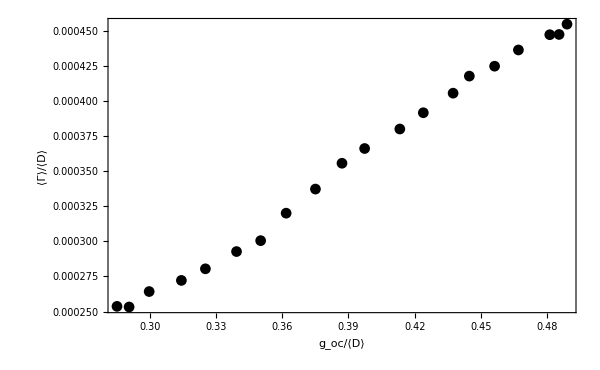

```mathematica
w1=ErrorListPlot[Table[t=MeanW[Emin,Emax,ic];{{SD[[ic,4]],t[[1]]/SD[[ic,3]] },ErrorBar[(t[[2]]/√t[[3]])]},{ic,1,Length[SD]}],Joined->False,PlotStyle->Black,Frame->True,PlotRange->All,FrameLabel->{"g_oc/⟨D⟩","⟨Γ⟩/⟨D⟩"},LabelStyle->{Large}]
```

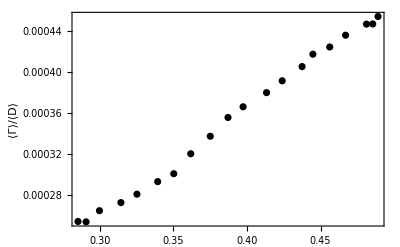

```mathematica
w2=ErrorListPlot[Table[t=MeanW[Emin,Emax,ic];{{SD[[ic,4]],t[[1]]/SD[[ic,3]]},ErrorBar[t[[2]]/√t[[3]]]},{ic,1,Length[SD]}],Joined->False,PlotStyle->Black,Frame->True,PlotRange->All,FrameLabel->{{"⟨Γ⟩/⟨D⟩",None},{None,"g_oc/⟨D⟩"}},Ticks->{{Automatic,Automatic},{None,Automatic}},LabelStyle->{Large}]
```

### Number variance of resonances

```mathematica
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.800","Table"];*)
AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];
```

```mathematica
AWD=DeleteCases[DeleteCases[AllWidthData,AllWidthData[[1]]],{}];
```

```mathematica
(*Sdat=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.700","Table"];*)
Sdat=Import["~/Code/Nchannel/Square/CODES/fort.700","Table"];
SD=DeleteCases[Sdat,Sdat[[1]]];
```

```mathematica
ic=1;iens=1;
DataKeep=Select[AWD,(#1[[3]]==ic && #1[[2]]==iens)&];
nw=Length[DataKeep]
```

47

```mathematica
rpos=Table[DataKeep[[i,5]],{i,1,nw}]
```

{0.000083029,0.00039376,0.0012347,0.0015253,0.0036934,0.0064785,0.010232,0.012343,0.020752,0.021354,0.024369,0.028362,0.033965,0.036304,0.039371,0.040149,0.040598,0.041835,0.043347,0.044646,0.047434,0.052028,0.055201,0.056172,0.056434,0.056939,0.059485,0.059618,0.059711,0.060474,0.063063,0.064526,0.065171,0.069507,0.074472,0.0757,0.077983,0.0806,0.081447,0.084907,0.085566,0.093864,0.094859,0.095088,0.098313,0.099171,0.099292}

```mathematica
tab1=Table[{DataKeep[[i,5]],i-1},{i,1,nw}];
f1=Interpolation[tab1,InterpolationOrder->0]
```

InterpolatingFunction[{{0.000083029, 0.099292}}, <>]

```mathematica
rpos
```

{0.000083029,0.00039376,0.0012347,0.0015253,0.0036934,0.0064785,0.010232,0.012343,0.020752,0.021354,0.024369,0.028362,0.033965,0.036304,0.039371,0.040149,0.040598,0.041835,0.043347,0.044646,0.047434,0.052028,0.055201,0.056172,0.056434,0.056939,0.059485,0.059618,0.059711,0.060474,0.063063,0.064526,0.065171,0.069507,0.074472,0.0757,0.077983,0.0806,0.081447,0.084907,0.085566,0.093864,0.094859,0.095088,0.098313,0.099171,0.099292}

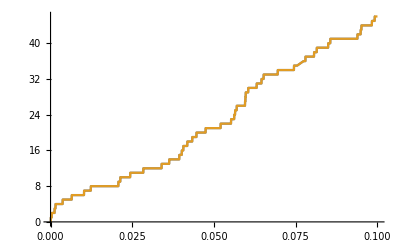

```mathematica
Emin=0.0;
Plot[{(i=FirstPosition[rpos,u_/;u>EE,0][[1]];i-1),f1[EE]},{EE,Emin,Emax}]
```

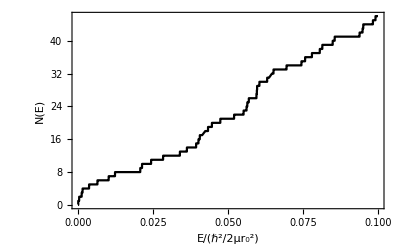

```mathematica
Plot[f1[EE],{EE,Emin,Emax},Frame->True,LabelStyle->Large,PlotStyle->Black,FrameLabel->{"E/(ℏ^2/2μr_0^2)","N(E)"},PlotPoints->100]
```

```mathematica
DataKeep=Select[AWDTrimmed,(#1[[3]]==ic && #1[[2]]==iens)&];
```

```mathematica
NumEns=10;
fall=Table[
DataKeep=Select[AWDTrimmed,(#1[[3]]==ic && #1[[2]]==iens)&];
nw=Length[DataKeep];
tab1=Table[{DataKeep[[i,5]],i-1},{i,1,nw}];
Interpolation[tab1,InterpolationOrder->0],{ic,1,Length[SD]},{iens,1,NumEns}];
```

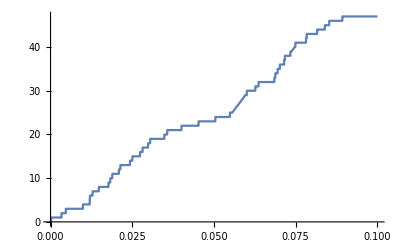

```mathematica
Plot[fall[[2,3]][Energy],{Energy,Emin,Emax},PlotPoints->100]
```

```mathematica
ΔEmax=(Emax-Emin)/10.0;
Erange=Table[EE,{EE,Emin,Emax,ΔEmax}]
nerange=Length[Erange]-1;
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1}

```mathematica
NERange[ΔE_,E0_,ic_,iens_]:=fall[[ic,iens]][E0+ΔE]-fall[[ic,iens]][E0]
```

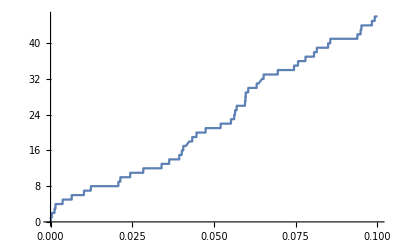

```mathematica
Plot[NERange[ΔE,0.0,1,1],{ΔE,Emin,Emax},PlotPoints->100]
```

```mathematica
nens=10
```

10

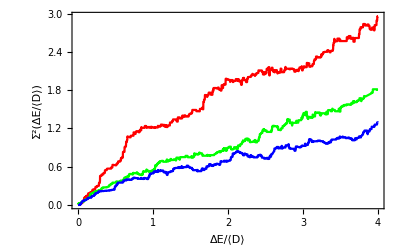

```mathematica
psigma2=Plot[Evaluate[Table[(
Sum[(NERange[DE,Erange[[ie]],ic,iens])^2,{iens,1,nens},{ie,1,nerange}]/(nens*nerange)
-(Sum[NERange[DE,Erange[[ie]],ic,iens],{iens,1,nens},{ie,1,nerange}]/(nens*nerange))^2)/.DE->DEOverD SD[[ic,3]],{ic,{1,4,20}}]],{DEOverD,0,4},
PlotStyle->{{Red},{Green},{Blue}},
Frame->True,
LabelStyle->Large,
FrameLabel->{"ΔE/⟨D⟩","Σ^2(ΔE/⟨D⟩)"}]
```

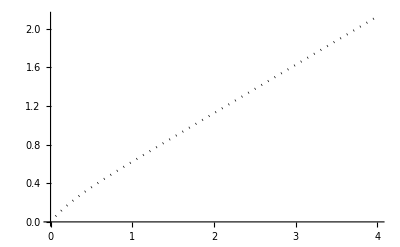

```mathematica
pSP=Plot[L/2+(1-Exp[-4 L])/8,{L,0,4},PlotStyle->{Black,Dotted}]
```

```mathematica
N[EulerGamma]
```

0.577216

```mathematica
Sig2Formula[β_,r_]:=2/(β π^2)(Log[β π r]+EulerGamma+1-Cos[β π r]-CosIntegral[β π r]) + r(1-2/π SinIntegral[β π r])
```

```mathematica
Sig2GOE[r_]:=2 Sig2Formula[2.0,r]+(SinIntegral[π r]/π)^2-1/π SinIntegral[π r]
```

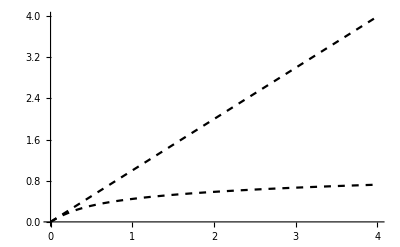

```mathematica
psigendcases=Plot[{Sig2Formula[0.001,r],Sig2GOE[r]},{r,0,4},PlotStyle->{{Black,Dashed},{Black,Dashed}}]
```

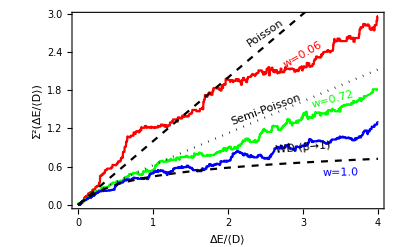

```mathematica
psig2=Show[psigma2,pSP,psigendcases,
Epilog->{
Text[Style[Rotate["Poisson",34 Degree],Medium],{2.5,2.7}],
Text[Style[Rotate["Semi-Poisson",20 Degree],Medium],{2.5,1.5}],
Text[Style[Rotate["WD (β→1)",5 Degree],Medium],{3.0,0.9}],
Text[Style[Rotate["w=0.06",30 Degree],{Medium,Red}],{3.0,2.35}],
Text[Style[Rotate["w=0.72",15 Degree],{Medium,Green}],{3.4,1.65}],
Text[Style[Rotate["w=1.0",1 Degree],{Medium,Blue}],{3.5,.50}]}]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/psigma2.pdf",psig2]
```

~/Code/Nchannel/Square/CODES/plots/psigma2.pdf

### What to expect for semi-poisson?

If we sample the semi-poisson distribution, what Brody parameter do we expect, and with what standard error?

```mathematica
cumsp[s_]:=Integrate[4s Exp[-2s],{s,0,s}]
```

```mathematica
cumsp[s]
```

ⅇ^(-2 s) (-1+ⅇ^(2 s)-2 s)

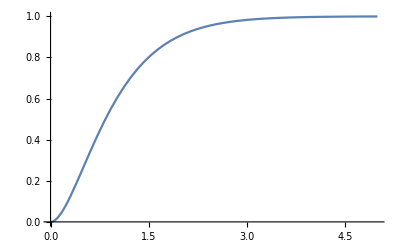

```mathematica
Plot[ⅇ^(-2 s) (-1+ⅇ^(2 s)-2 s),{s,0,5}]
```

```mathematica
spacing[u_]:=s/.FindRoot[u==ⅇ^(-2 s) (-1+ⅇ^(2 s)-2 s),{s,0.5},PrecisionGoal->20][[1]]
```

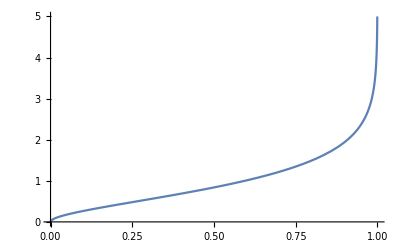

```mathematica
Plot[spacing[u],{u,0,1},PlotRange->{0,5}]
```

```mathematica
spacing[.9999]
```

5.87819

```mathematica
SPSample[n_]:=Module[{u,z},u=RandomReal[{0,0.9999999},n];Map[spacing,u]]
```

```mathematica
w0=0.74;
NP=100000;
dx=0.2;
Bins=Table[t,{t,0,5,dx}];
samp=SPSample[NP];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
SD[[9,5]]
```

0.66924

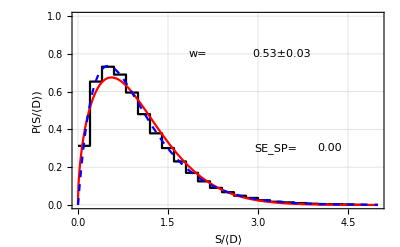

```mathematica
bc=BinCounts[samp,{Bins}]/NP/dx;
bnorm=Table[{(Bins[[i]]),bc[[i]]},{i,1,Length[Bins]-1}];
bfit=Table[{(Bins[[i]]+Bins[[i+1]])/2,bc[[i]]},{i,1,Length[Bins]-1}];
ph=ListPlot[bnorm,InterpolationOrder->0,Joined->True,PlotStyle->Black];
psp=Plot[4s Exp[-2s],{s,0,5},PlotStyle->{Blue,Dashed}];
nlm=NonlinearModelFit[bfit,{PBrody[z,w]},{{w,w0}},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.9999];
pb=Plot[PBrody[z,w/.nlm["BestFitParameters"]],{z,0,5},PlotStyle->{Red}];
Show[{ph,pb,psp},PlotRange->{0,1},Frame->True,GridLines->Automatic,FrameLabel->{"S/⟨D⟩","P(S/⟨D⟩)"},LabelStyle->Large,Epilog->{
Text[Style["SE_SP= ",Large],{3.3,0.3}],
Text[Style["w=",Large],{2,0.8}],
Text[Style[NumberForm[FitError[SemiPoisson,bfit,Null],{2,2}],Large],{4.2,0.3}],Text[Style[NumberForm[w/.nlm["BestFitParameters"],{2,2}]±NumberForm[FitError[PBrody,bfit,w/.nlm["BestFitParameters"]],{2,2}],Large],{3.4,0.8}]}]
```

```mathematica
PBrody[z,0.6]
```

1.34356 ⅇ^(-0.839727 z^1.6) z^0.6

```mathematica
FitError[PBrody,bfit,.7]
```

0.049557